## Switching Time Analysis Pile Driver Ashwin & Aaron

```mathematica
casetimes = {(√(2 vop^2+4 a l)-2 vop)/(2 a),2(√(2 vop^2+4 a l)-2 vop)/(2 a),3(√(2 vop^2+4 a l)-2 vop)/(2 a),4(√(2 vop^2+4 a l)-2 vop)/(2 a),5(√(2 vop^2+4 a l)-2 vop)/(2 a)};

deltaT[ts_,vop_,a_,m_,k_,l_]:=Piecewise[{{deltaTc1[ts,vop,a,l], ts<casetimes⟦1⟧}, {deltaTc2[ts,vop,a,m,k,l], ts<casetimes⟦2⟧}, {deltaTc3[ts,vop,a,m,k,l], ts<casetimes⟦3⟧}, {deltaTc4[ts,vop,a,m,k,l], ts<casetimes⟦4⟧}, {deltaTc5[ts,vop,a,m,k,l], ts<casetimes⟦5⟧}, {deltaTc6[ts,vop,a,m,k,l], True}}]
```

```mathematica
deltaTc1[ts_,vop_,a_,l_]:=2 ts+vop/a+√(2((vop/a+ts)^2-vop^2/(2 a^2)))
deltaTc2[ts_,vop_,a_,m_,k_,l_]:=Module[{ω},ω = √(k/m);

2 ts+vop/a+√(2((vop/a+ts)^2-vop^2/(2 a^2)))+ω
]
```

## Simplify math

```mathematica
FullSimplify[2 ts+vop/a+√(2((vop/a+ts)^2-vop^2/(2 a^2)))]
```

2 ts+vop/a+√((2 a^2 ts^2+4 a ts vop+vop^2)/a^2)

```mathematica
ω = √(k/m);

FullSimplify[2 ts+vop/a+√(2((vop/a+ts)^2-vop^2/(2 a^2)))+ω]
```

√(k/m)+2 ts+vop/a+√((2 a^2 ts^2+4 a ts vop+vop^2)/a^2)

## Make simple plot of ΔT vs t_s

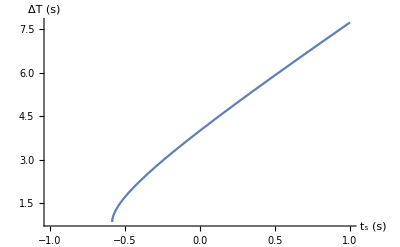

```mathematica
a=1;
vop = 1/2;
l = 0.1;
Plot[deltaTc1[ts,a,vop,l],{ts,-1,1},
AxesLabel->{"t_s (s)","ΔT (s)"}
]
(*TODO: call deltaT[ts,vop,a,m,k,l] instead!*)
```

## Make plot of ΔT vs t_s

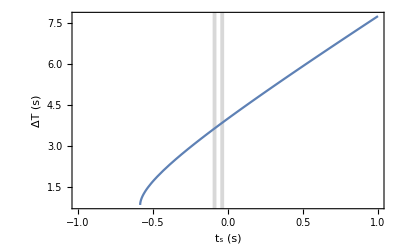

```mathematica
a=1;
vop = 1/2;
l = 0.1;
Plot[deltaTc1[ts,a,vop,l],{ts,-1,1},
Frame->{True,True,False,False},FrameLabel->{"t_s (s)","ΔT (s)"},
(*Epilog->{Gray,Thin,Table[Line[{{tc,0},{tc,100}}],{ tc, casetimes }]}*)
Prolog-> {Gray,Opacity[0.3],Thin,Table[Rectangle[{casetimes⟦2tc-1⟧,0},{casetimes⟦2tc⟧,100}],{ tc, 1,Floor[Length[casetimes]/2] }]}

]
(*TODO: call deltaT[ts,vop,a,m,k,l] instead!*)
```

```mathematica
casetimes
```

{0.974342,1.94868,2.92302,3.89737,4.87171}

## (simple) Make plot of ΔT vs v_(0^+)

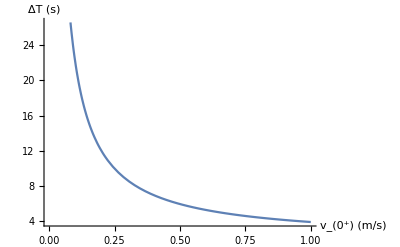

```mathematica
a=1;
ts = 1/2;
l = 0.1;
Plot[deltaTc1[ts,a,vop,l],{vop,0,1},
AxesLabel->{"v_(0^+) (m/s)","ΔT (s)"}
]
(*TODO: call deltaT[ts,vop,a,m,k,l] instead!*)
```

## better plot of ΔT vs v_(0^+)

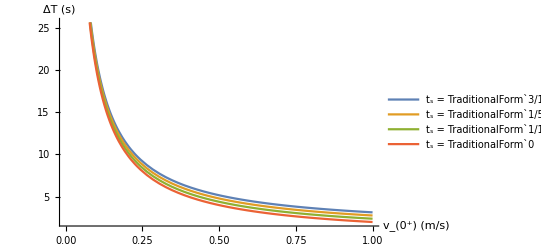

```mathematica
a=1;
ts = 1/2;
l = 0.1;
tsVals = {3/10,2/10,1/10,0/10};
Clear[vop]
Plot[Evaluate[Table[deltaTc1[ts,a,vop,l],{ts,tsVals}]],{vop,0,1},
AxesLabel->{"v_(0^+) (m/s)","ΔT (s)"},
PlotLegends->Table[StringForm["t_s = ``",ts],{ts,tsVals}]
]
(*TODO: call deltaT[ts,vop,a,m,k,l] instead!*)
```